```mathematica
(* Returns a matrix where each column is a perturbed eigenstate *)
NonDegPerturbationTheoryStates[E0_(*List of zero order energies*),V_(*Perturbation Hamiltonian*),ORDER_:1 (* Order in Perturbation Theory, MAXIMUM 1 *)]:=Module[{DIMS,n,k},
DIMS=Length@E0;
States=IdentityMatrix[DIMS];
If[ORDER≥1,States+=Table[If[k≠n,V[[k,n]]/(E0[[n]]-E0[[k]]),0],{k,DIMS},{n,DIMS}],0];
States
]
(* Returns a list with eigenenergies *)
NonDegPerturbationTheoryEnergies[E0_(*List of zero order energies*),V_(*Perturbation Hamiltonian*),ORDER_:1 (* Order in Perturbation Theory, MAXIMUM 2 *)]:=Module[{DIMS,n,k},
DIMS=Length@E0;
Energies=E0;
If[ORDER≥1,Energies+=Diagonal[V],0];
If[ORDER≥2,Energies+=Table[Sum[If[k≠n,(V[[n,k]]*V[[k,n]])/(E0[[n]]-E0[[k]]),0],{k,DIMS}],{n,DIMS}],0];
Energies
]
```

# Flip-Flop Cavity Coupling
We start be defining our Hamiltonian. Our states are ordered 00,01,10,11

```mathematica
H1=δ*({{-1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}});H2=gf*({{0, √n0, √n0, 0}, {√n0, 0, 0, √(n0-1)}, {√n0, 0, 0, √(n0-1)}, {0, √(n0-1), √(n0-1), 0}});H=H1+H2
```

```mathematica
(//.subNum)
```

Our first order of business is to deal with the degeneracy of the 01 and 10 states.

```mathematica
R1=({{1, 0, 0, 0}, {0, 1/√2, 1/√2, 0}, {0, -1/√2, 1/√2, 0}, {0, 0, 0, 1}});
H1=Inverse[R1].H1.R1;
H2=Inverse[R1].H2.R1;
H=H1+H2
```

(-δ | 0 | √2 gf √n0 | 0
0 | 0 | 0 | 0
√2 gf √n0 | 0 | 0 | √2 gf √(n0-1)
0 | 0 | √2 gf √(n0-1) | δ)

```mathematica
({{-δ, 0, √2 √n0 gf, 0}, {0, 0, 0, 0}, {√2 √n0 gf, 0, 0, √2 √(n0-1) gf}, {0, 0, √2 √(n0-1) gf, δ}})
```

(-δ | 0 | √2 gf √n0 | 0
0 | 0 | 0 | 0
√2 gf √n0 | 0 | 0 | √2 gf √(n0-1)
0 | 0 | √2 gf √(n0-1) | δ)

We immediately see that the |01-10>/√2 state is now decoupled from the other three states, making it an eigenstate of the total Hamiltonian. So we now reduce our state space down to the remaining three.

```mathematica
H1=H1[[{1,3,4},{1,3,4}]];
H2=H2[[{1,3,4},{1,3,4}]];
H=H1+H2
```

(-δ | √2 gf √n0 | 0
√2 gf √n0 | 0 | √2 gf √(n0-1)
0 | √2 gf √(n0-1) | δ)

```mathematica
({{-δ, √2 √n0 gf, 0}, {√2 √n0 gf, 0, √2 √(n0-1) gf}, {0, √2 √(n0-1) gf, δ}})
```

This 3x3 Hamiltonian is not exactly solvable. We’ll have to take different limiting cases.
 A. δ = 0
 B. δ<<g
 C. δ ~ g
 D. δ>>g
 The first case is exactly solvable.

```mathematica
(* CASE 1: δ=0 *)
HA=H//.{δ->0}
```

(0 | √2 gf √n0 | 0
√2 gf √n0 | 0 | √2 gf √(n0-1)
0 | √2 gf √(n0-1) | 0)

```mathematica
RA=({{Cos[ϕ]/√2, -Sin[ϕ], Cos[ϕ]/√2}, {-1/√2, 0, 1/√2}, {Sin[ϕ]/√2, Cos[ϕ], Sin[ϕ]/√2}});
```

```mathematica
EA=Inverse[RA].HA.RA//.{Cos[ϕ]-> (√n0)/(√(2n0-1)),Sin[ϕ]-> (√(n0-1))/(√(2n0-1))}//FullSimplify//Diagonal
```

{-gf √(4 n0-2),0,gf √(4 n0-2)}

```mathematica
{√(4 n0-2) (-gf),0,√(4 n0-2) gf}
```

To get back our original basis, we append back in the 01-10 state. And then left multiply by R1

```mathematica
RAtrue=R1.(Append[Append[RA,{0,0,0}]//Transpose,{0,0,0,1}][[{1,4,2,3},{1,4,2,3}]]//Transpose)
EAtrue=Insert[EA,0,2]
```

((cos(ϕ))/(√2) | 0 | -sin(ϕ) | (cos(ϕ))/(√2)
-1/2 | 1/(√2) | 0 | 1/2
-1/2 | -1/(√2) | 0 | 1/2
(sin(ϕ))/(√2) | 0 | cos(ϕ) | (sin(ϕ))/(√2))

{-gf √(4 n0-2),0,0,gf √(4 n0-2)}

The second can be solved by treating δ as the perturbation. Then we can use the solution to Case A as the unperturbed basis.

```mathematica
HB=DiagonalMatrix[EA];VB=Inverse[RA].H1.RA//Simplify;
RB=NonDegPerturbationTheoryStates[Diagonal[HB],VB,1]//Simplify
EB=NonDegPerturbationTheoryEnergies[Diagonal[HB],VB,2]//Simplify
```

(1 | -(δ (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 gf √(4 n0-2)) | -(δ (sin(4 ϕ)+6 cos(2 ϕ)))/(16 gf √(4 n0-2))
(δ (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1)) | 1 | -(δ (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))
(δ (sin(4 ϕ)+6 cos(2 ϕ)))/(16 gf √(4 n0-2)) | (δ (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 gf √(4 n0-2)) | 1)

```mathematica
{1/(128 gf √(4 n0-2))(-δ^2 (sin(4 ϕ)+6 cos(2 ϕ))^2-2 √2 δ^2 (1-2 sin(ϕ) cos(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ)))+256 gf^2 (1-2 n0)-16 δ gf √(2 n0-1) (sin(ϕ)+cos(ϕ)) (3 √2 sin(ϕ)+8 sin(2 ϕ)+√2 sin(3 ϕ)-3 √2 cos(ϕ)+√2 cos(3 ϕ))),(δ (cos(ϕ)-sin(ϕ))^3 (sin(ϕ)+cos(ϕ)) (δ sin(ϕ)+δ sin(3 ϕ)+δ cos(ϕ)-δ cos(3 ϕ)-2 gf √(2 n0-1)))/(4 gf √(2 n0-1)),1/(128 gf √(4 n0-2))(δ^2 (sin(4 ϕ)+6 cos(2 ϕ))^2+2 √2 δ^2 (1-2 sin(ϕ) cos(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ)))+256 gf^2 (2 n0-1)-16 δ gf √(2 n0-1) (sin(ϕ)+cos(ϕ)) (3 √2 sin(ϕ)-8 sin(2 ϕ)+√2 sin(3 ϕ)-3 √2 cos(ϕ)+√2 cos(3 ϕ)))}
```

{1/(128 gf √(4 n0-2))(-δ^2 (sin(4 ϕ)+6 cos(2 ϕ))^2-2 √2 δ^2 (1-2 sin(ϕ) cos(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ)))+256 gf^2 (1-2 n0)-16 δ gf √(2 n0-1) (sin(ϕ)+cos(ϕ)) (3 √2 sin(ϕ)+8 sin(2 ϕ)+√2 sin(3 ϕ)-3 √2 cos(ϕ)+√2 cos(3 ϕ))),(δ (cos(ϕ)-sin(ϕ))^3 (sin(ϕ)+cos(ϕ)) (δ sin(ϕ)+δ sin(3 ϕ)+δ cos(ϕ)-δ cos(3 ϕ)-2 gf √(2 n0-1)))/(4 gf √(2 n0-1)),1/(128 gf √(4 n0-2))(δ^2 (sin(4 ϕ)+6 cos(2 ϕ))^2+2 √2 δ^2 (1-2 sin(ϕ) cos(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ)))+256 gf^2 (2 n0-1)-16 δ gf √(2 n0-1) (sin(ϕ)+cos(ϕ)) (3 √2 sin(ϕ)-8 sin(2 ϕ)+√2 sin(3 ϕ)-3 √2 cos(ϕ)+√2 cos(3 ϕ)))}

These states are in the eigenbasis of HA though so to get them in terms of 00, 01+10, and 11, we have to left multiply by RA.

```mathematica
RBsemitrue=RA.RB;
RBtrue=R1.(Append[Append[RBsemitrue,{0,0,0}]//Transpose,{0,0,0,1}][[{1,4,2,3},{1,4,2,3}]]//Transpose)
EBtrue=Insert[EB,0,2]
```

(-sin(ϕ) ((δ (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-1/(√2))+(cos(ϕ) ((δ cos(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1))+(cos(ϕ))/(√2)))/(√2)+(cos(ϕ) ((δ sin(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1))+(sin(ϕ))/(√2)))/(√2) | 0 | -sin(ϕ) ((δ (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+(δ (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2)))+(cos(ϕ) ((δ cos(ϕ) (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))-(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))-sin(ϕ)))/(√2)+(cos(ϕ) ((δ sin(ϕ) (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))-(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+cos(ϕ)))/(√2) | -sin(ϕ) ((δ (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+1/(√2))+(cos(ϕ) (-(δ cos(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))+(cos(ϕ))/(√2)))/(√2)+(cos(ϕ) (-(δ sin(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))+(sin(ϕ))/(√2)))/(√2)
1/2 (-(δ cos(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1))-(cos(ϕ))/(√2))+1/2 ((δ sin(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1))+(sin(ϕ))/(√2)) | 1/(√2) | 1/2 (-(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+sin(ϕ))+1/2 ((δ sin(ϕ) (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))-(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+cos(ϕ)) | 1/2 ((δ cos(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))-(cos(ϕ))/(√2))+1/2 (-(δ sin(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))+(sin(ϕ))/(√2))
1/2 (-(δ cos(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1))-(cos(ϕ))/(√2))+1/2 ((δ sin(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1))+(sin(ϕ))/(√2)) | -1/(√2) | 1/2 (-(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+sin(ϕ))+1/2 ((δ sin(ϕ) (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))-(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+cos(ϕ)) | 1/2 ((δ cos(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))-(cos(ϕ))/(√2))+1/2 (-(δ sin(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))+(sin(ϕ))/(√2))
cos(ϕ) ((δ (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-1/(√2))+(sin(ϕ) ((δ cos(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1))+(cos(ϕ))/(√2)))/(√2)+(sin(ϕ) ((δ sin(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))))/(8 gf √(2 n0-1))+(sin(ϕ))/(√2)))/(√2) | 0 | cos(ϕ) ((δ (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+(δ (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2)))+(sin(ϕ) ((δ cos(ϕ) (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))-(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))-sin(ϕ)))/(√2)+(sin(ϕ) ((δ sin(ϕ) (cos(ϕ)-sin(ϕ)) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))-(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ))))/(8 √2 gf √(4 n0-2))+cos(ϕ)))/(√2) | cos(ϕ) ((δ (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+1/(√2))+(sin(ϕ) (-(δ cos(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))+(δ sin(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))+(cos(ϕ))/(√2)))/(√2)+(sin(ϕ) (-(δ sin(ϕ) (sin(4 ϕ)+6 cos(2 ϕ)))/(16 √2 gf √(4 n0-2))-(δ cos(ϕ) (cos(ϕ)-sin(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))))/(8 gf √(2 n0-1))+(sin(ϕ))/(√2)))/(√2))

{1/(128 gf √(4 n0-2))(-δ^2 (sin(4 ϕ)+6 cos(2 ϕ))^2-2 √2 δ^2 (1-2 sin(ϕ) cos(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (2 √2 cos(ϕ)+cos(2 ϕ))) ((8 sin(ϕ)+√2) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ)))+256 gf^2 (1-2 n0)-16 δ gf √(2 n0-1) (sin(ϕ)+cos(ϕ)) (3 √2 sin(ϕ)+8 sin(2 ϕ)+√2 sin(3 ϕ)-3 √2 cos(ϕ)+√2 cos(3 ϕ))),0,(δ (cos(ϕ)-sin(ϕ))^3 (sin(ϕ)+cos(ϕ)) (δ sin(ϕ)+δ sin(3 ϕ)+δ cos(ϕ)-δ cos(3 ϕ)-2 gf √(2 n0-1)))/(4 gf √(2 n0-1)),1/(128 gf √(4 n0-2))(δ^2 (sin(4 ϕ)+6 cos(2 ϕ))^2+2 √2 δ^2 (1-2 sin(ϕ) cos(ϕ)) (cos(ϕ)+cos(3 ϕ)+2 sin(ϕ) (cos(2 ϕ)-2 √2 cos(ϕ))) ((√2-8 sin(ϕ)) cos(ϕ)+√2 (cos(3 ϕ)+2 sin(ϕ) cos(2 ϕ)))+256 gf^2 (2 n0-1)-16 δ gf √(2 n0-1) (sin(ϕ)+cos(ϕ)) (3 √2 sin(ϕ)-8 sin(2 ϕ)+√2 sin(3 ϕ)-3 √2 cos(ϕ)+√2 cos(3 ϕ)))}

We can also do the same for case D except g is now the perturbation

```mathematica
HD=H1;VD=H2;
RD=NonDegPerturbationTheoryStates[Diagonal[HD],VD,1]//Simplify
ED=NonDegPerturbationTheoryEnergies[Diagonal[HD],VD,2]//Simplify
```

(1 | (√2 gf √n0)/δ | 0
-(√2 gf √n0)/δ | 1 | (√2 gf √(n0-1))/δ
0 | -(√2 gf √(n0-1))/δ | 1)

{-δ-(2 gf^2 n0)/δ,(2 gf^2)/δ,δ+(2 gf^2 (n0-1))/δ}

```mathematica
RDtrue=R1.(Append[Append[RD,{0,0,0}]//Transpose,{0,0,0,1}][[{1,4,2,3},{1,4,2,3}]]//Transpose)
EDtrue=Insert[ED,0,2]
```

(1 | 0 | (√2 gf √n0)/δ | 0
-(gf √n0)/δ | 1/(√2) | 1/(√2) | (gf √(n0-1))/δ
-(gf √n0)/δ | -1/(√2) | 1/(√2) | (gf √(n0-1))/δ
0 | 0 | -(√2 gf √(n0-1))/δ | 1)

{-δ-(2 gf^2 n0)/δ,0,(2 gf^2)/δ,δ+(2 gf^2 (n0-1))/δ}

Let us now define our two sources of noise

```mathematica
hL=({{w03+w30+w33-2*n0*(gc^2*(w30+w33))/δc^2, 0, -√n0*gc*wp/δc, 0}, {0, w03+w30+w33-2(n0-1)(gc^2*(w30+w33))/δc^2, -(gc*gf*wp)/(δc*(δc-δf)), -√(n0-1)*gc*wp/δc}, {-√n0*gc*wp/δc, -(gc*gf*wp)/(δc*(δc-δf)), -w03+w30-w33-2(n0-1)(gc^2*(w30+w33))/δc^2-2(gc*gf*wp)/(δc*(δc-δf)), 0}, {0, -√(n0-1)*gc*wp/δc, 0, -w03+w30-w33-2(n0-1)(gc*gf*wp)/(δc*(δc-δf))}});
hR=({{w03+w30+w33-2*n0*(gc^2*(w30+w33))/δc^2, -√n0*gc*wp/δc, 0, 0}, {-√n0*gc*wp/δc, -w03+w30-w33-2(n0-1)(gc^2*(w30+w33))/δc^2-2(gc*gf*wp)/(δc*(δc-δf)), -(gc*gf*wp)/(δc*(δc-δf)), 0}, {0, -(gc*gf*wp)/(δc*(δc-δf)), w03+w30+w33-2(n0-1)(gc^2*(w30+w33))/δc^2, -√(n0-1)*gc*wp/δc}, {0, 0, -√(n0-1)*gc*wp/δc, -w03+w30-w33-2(n0-1)(gc*gf*wp)/(δc*(δc-δf))}});
```

Next we define some functions to determine the time evolution
Γ_ij^2=(<a| R^-1.hL.R|a>-<b| R^-1.hL.R|b>)^2 + (<a| R^-1.hR.R|a>-<b| R^-1.hR.R|b>)^2
W_ij = E_a- E_b
C_ij = R_aj R^-1_jp R_bk R^-1_kq rho_pq

```mathematica
ρ0=({{0, 0, 0, 0}, {0, α^2, α*β, 0}, {0, α*β, β^2, 0}, {0, 0, 0, 0}});
c[a_,b_,R_,ρ_]:=Table[Sum[R[[a,j]]*Inverse[R][[j,p]]*R[[b,k]]*Inverse[R][[k,q]]*ρ[[p,q]],{p,4},{q,4}],{j,4},{k,4}]//UpperTriangularize;
W[w_]:=Table[w[[j]]-w[[k]],{j,4},{k,4}]//UpperTriangularize;
Γ[h_,R_]:=Sqrt[Sum[Outer[Subtract,Diagonal[Inverse[R].h[[j]].R],Diagonal[Inverse[R].h[[j]].R]]^2 ,{j,Length@h}]]//UpperTriangularize;
```

```mathematica
EAtrue
RAtrue
Series[Total[Diagonal[c[2,2,RAtrue,ρ0]//.{α->1,β->0}]],{δ,0,2}]//Simplify//Normal
(Series[c[2,2,RAtrue,ρ0]//.{α->1,β->0},{δ,0,2}]//Flatten)[[{2,3,4,7,8,12}]]//Simplify//Normal
(Series[W[EAtrue],{δ,0,2}]//Flatten)[[{2,3,4,7,8,12}]]//Simplify//Normal
(Series[Γ[{hL,hR},RAtrue]^2,{δ,0,2}]//Flatten)[[{2,3,4,7,8,12}]]//Simplify//Normal//StandardForm
```

{-gf √(4 n0-2),0,0,gf √(4 n0-2)}

((cos(ϕ))/(√2) | 0 | -sin(ϕ) | (cos(ϕ))/(√2)
-1/2 | 1/(√2) | 0 | 1/2
-1/2 | -1/(√2) | 0 | 1/2
(sin(ϕ))/(√2) | 0 | cos(ϕ) | (sin(ϕ))/(√2))

3/8

{1/8,0,1/16,0,1/8,0}

{-gf √(4 n0-2),-gf √(4 n0-2),-2 gf √(4 n0-2),0,-gf √(4 n0-2),-gf √(4 n0-2)}

{1/(2 δc^4 (δc-δf)^2)(-√2 gc √n0 wp δc (δc-δf) Cos[ϕ]+(-gc gf (-1+n0) wp δc+gc^2 n0 (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)) Cos[2 ϕ]+gc (gf (1+n0) wp δc-gc (-2+n0) (w30+w33) (δc-δf)-√2 √(-1+n0) wp δc (δc-δf) Sin[ϕ]))^2,1/(2 δc^4 (δc-δf)^2)(√2 gc √n0 wp δc (δc-δf) Cos[ϕ]-3 (-gc gf (-1+n0) wp δc+gc^2 n0 (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)) Cos[2 ϕ]+gc (gf (-3+n0) wp δc-gc (-2+n0) (w30+w33) (δc-δf)+√2 √(-1+n0) wp δc (δc-δf) Sin[ϕ]))^2,(2 gc^2 wp^2 (-1+2 n0+Cos[2 ϕ]+2 √(-1+n0) √n0 Sin[2 ϕ]))/δc^2,1/(δc^4 (δc-δf)^2)2 (gc (-gf (-1+n0) wp δc+gc (-2+n0) (w30+w33) (δc-δf))+(-gc gf (-1+n0) wp δc+gc^2 n0 (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)) Cos[2 ϕ])^2,1/(2 δc^4 (δc-δf)^2)(√2 gc √n0 wp δc (δc-δf) Cos[ϕ]+(-gc gf (-1+n0) wp δc+gc^2 n0 (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)) Cos[2 ϕ]+gc (gf (1+n0) wp δc-gc (-2+n0) (w30+w33) (δc-δf)+√2 √(-1+n0) wp δc (δc-δf) Sin[ϕ]))^2,1/(2 δc^4 (δc-δf)^2)(√2 gc √n0 wp δc (δc-δf) Cos[ϕ]+3 (-gc gf (-1+n0) wp δc+gc^2 n0 (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)) Cos[2 ϕ]+gc (-gf (-3+n0) wp δc+gc (-2+n0) (w30+w33) (δc-δf)+√2 √(-1+n0) wp δc (δc-δf) Sin[ϕ]))^2}

```mathematica
EDtrue
RDtrue
Series[Total[Diagonal[c[2,2,RDtrue,ρ0]//.{α->1,β->0}]],{δ,∞,2}]//Simplify//Normal
(Series[c[2,2,RDtrue,ρ0]//.{α->1,β->0},{δ,∞,2}]//Flatten)[[{2,3,4,7,8,12}]]//Simplify//Normal
(Series[W[EDtrue],{δ,∞,2}]//Flatten)[[{2,3,4,7,8,12}]]//Simplify//Normal
(Series[Γ[{hL,hR},RDtrue]^2,{δ,∞,2}]//Flatten)[[{2,3,4,7,8,12}]]//Simplify//Normal//StandardForm
```

{-δ-(2 gf^2 n0)/δ,0,(2 gf^2)/δ,δ+(2 gf^2 (n0-1))/δ}

(1 | 0 | (√2 gf √n0)/δ | 0
-(gf √n0)/δ | 1/(√2) | 1/(√2) | (gf √(n0-1))/δ
-(gf √n0)/δ | -1/(√2) | 1/(√2) | (gf √(n0-1))/δ
0 | 0 | -(√2 gf √(n0-1))/δ | 1)

(gf^2 (1-2 n0))/δ^2+1/2

{(gf^2 n0)/(2 δ^2),(gf^2 n0)/(2 δ^2),0,(gf^2 (1-2 n0))/(2 δ^2)+1/4,(gf^2 (n0-1))/(2 δ^2),(gf^2 (n0-1))/(2 δ^2)}

{-δ-(2 gf^2 n0)/δ,-δ-(2 gf^2 (n0+1))/δ,(2 gf^2 (1-2 n0))/δ-2 δ,-(2 gf^2)/δ,-δ-(2 gf^2 (n0-1))/δ,-δ-(2 gf^2 (n0-2))/δ}

{-(8 gc gf n0 wp (2 gc^2 (w30+w33)-(w03+w33) δc^2))/(δ δc^3)+(2 (-2 gc^2 (w30+w33)+(w03+w33) δc^2)^2)/δc^4+(8 gf^2 n0 (gc^2 n0 wp^2 δc^2-((-2 gc^2 (w30+w33)+(w03+w33) δc^2) (2 gc gf wp δc-2 gc^2 (w30+w33) (δc-δf)+(w03+w33) δc^2 (δc-δf)))/(δc-δf)))/(δ^2 δc^4),1/(δ^2 δc^4)8 ((gc gf wp+gc gf n0 wp)^2 δc^2+1/(δc-δf)^2 gf^2 (-2 gc gf wp δc+2 gc^2 (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)) (-2 gc gf (2-5 n0+n0^2) wp δc+2 gc^2 (1-4 n0+n0^2) (w30+w33) (δc-δf)+(1+n0) (w03+w33) δc^2 (δc-δf)))+(2 (2 gc gf wp δc-2 gc^2 (w30+w33) (δc-δf)+(w03+w33) δc^2 (δc-δf))^2)/(δc^4 (δc-δf)^2)-(8 gc gf (1+n0) wp (-2 gc gf wp δc+2 gc^2 (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)))/(δ δc^3 (δc-δf)),1/(δ^2 δc^2)8 ((gc gf wp-2 gc gf n0 wp)^2-1/(δc^2 (δc-δf)^2)2 gf^2 (gc gf (-1+n0) wp δc-gc^2 n0 (w30+w33) (δc-δf)+(w03+w33) δc^2 (δc-δf)) (2 gc gf (2-2 n0+n0^2) wp δc-2 gc^2 (1-n0+n0^2) (w30+w33) (δc-δf)+(-1+2 n0) (w03+w33) δc^2 (δc-δf)))+(16 gc gf (-1+2 n0) wp (w03+w33-(gc^2 n0 (w30+w33))/δc^2+(gc gf (-1+n0) wp)/(δc (δc-δf))))/(δ δc)+8 (w03+w33-(gc^2 n0 (w30+w33))/δc^2+(gc gf (-1+n0) wp)/(δc (δc-δf)))^2,(8 gc^2 gf^2 wp^2)/(δc^2 (δc-δf)^2)-1/(δ^2 δc^3 (δc-δf)^2)8 gc gf^2 wp (-gc wp δc (4 gf^2 (2-4 n0+n0^2)+(δc-δf)^2)+4 gc^2 gf (1-3 n0+n0^2) (w30+w33) (δc-δf)+2 gf (w03+w33) δc^2 (δc-δf))+(16 gc^2 gf^2 wp^2)/(δ δc^2 (δc-δf)),1/(δ^2 δc^2)8 gf^2 (-1+n0) (gc^2 (-1+n0) wp^2+1/(δc^2 (δc-δf)^2)(-2 gc gf (-2+n0) wp δc+2 gc^2 (-1+n0) (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)) (2 gc gf (-1+n0) wp δc-2 gc^2 (-1+n0) (w30+w33) (δc-δf)+(w03+w33) δc^2 (δc-δf)))+(2 (2 gc gf (-1+n0) wp δc-2 gc^2 (-1+n0) (w30+w33) (δc-δf)+(w03+w33) δc^2 (δc-δf))^2)/(δc^4 (δc-δf)^2)-(8 gc gf (-1+n0) wp (-2 gc gf (-1+n0) wp δc+2 gc^2 (-1+n0) (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)))/(δ δc^3 (δc-δf)),1/δ^2((8 (-2 gc gf wp+gc gf n0 wp)^2)/δc^2-1/(δc^4 (δc-δf)^2)8 gf^2 (2 gc gf (-2+n0) wp δc-2 gc^2 (-1+n0) (w30+w33) (δc-δf)+(w03+w33) δc^2 (δc-δf)) (2 gc gf (4-7 n0+2 n0^2) wp δc-2 gc^2 (2-5 n0+2 n0^2) (w30+w33) (δc-δf)+(-2+n0) (w03+w33) δc^2 (δc-δf)))+(2 (2 gc gf (-2+n0) wp δc-2 gc^2 (-1+n0) (w30+w33) (δc-δf)+(w03+w33) δc^2 (δc-δf))^2)/(δc^4 (δc-δf)^2)-(8 gc gf (-2+n0) wp (-2 gc gf (-2+n0) wp δc+2 gc^2 (-1+n0) (w30+w33) (δc-δf)-(w03+w33) δc^2 (δc-δf)))/(δ δc^3 (δc-δf))}

```mathematica
(Series[Γ[{hL},RDtrue]^2,{δ,∞,2}]//Normal)//.{δ-> δf+(2 gc^2)/δc^2,gf-> 0.005,wxy-> wp*gc/δc,ϕ->ArcTan[√n0,√(-1+n0)],n0->4,gc->0.05,wp->0.002,δc->(11.4-wcav),δf->(10.8-wcav),wcav->5,w03->0,w33->0,w30->0}
```

(0 | 1.16114×10^-14 | 1.56113×10^-13 | 9.40552×10^-13
0 | 0 | 8.25737×10^-14 | 7.43156×10^-13
0 | 0 | 0 | 3.3029×10^-13
0 | 0 | 0 | 0)

```mathematica
(Inverse[RDtrue].hL.RDtrue)[[{1,3,4,2},{1,3,4,2}]]//.{δ-> δf+(2 gc^2)/δc^2,gf-> 0.005,wxy-> wp*gc/δc,ϕ->ArcTan[√n0,√(-1+n0)],n0->4,gc->0.05,wp->0.002,δc->(11.4-wcav),δf->(10.8-wcav),wcav->5,w03->0,w33->0,w30->0}
```

(1.07754×10^-7 | -0.0000220964 | -3.09761×10^-12 | 0.0000220965
-0.0000220962 | -2.87356×10^-7 | -0.0000191354 | 2.24493×10^-7
1.89554×10^-12 | -0.0000191356 | -8.62065×10^-7 | -0.0000191362
0.0000220968 | 2.24495×10^-7 | -0.0000191364 | 0.)

```mathematica
hL//.{δ-> δf+(2 gc^2)/δc^2,gf-> 0.005,wxy-> wp*gc/δc,ϕ->ArcTan[√n0,√(-1+n0)],n0->4,gc->0.05,wp->0.002,δc->(11.4-wcav),δf->(10.8-wcav),wcav->5,w03->0,w33->0,w30->0}//N
```

(0. | 0. | -0.00003125 | 0.
0. | 0. | -1.30208×10^-7 | -0.0000270633
-0.00003125 | -1.30208×10^-7 | -2.60417×10^-7 | 0.
0. | -0.0000270633 | 0. | -7.8125×10^-7)

```mathematica
RDtrue//.{δ-> δf+(2 gc^2)/δc^2,gf-> 0.005,wxy-> wp*gc/δc,ϕ->ArcTan[√n0,√(-1+n0)],n0->4,gc->0.05,wp->0.002,δc->(11.4-wcav),δf->(10.8-wcav),wcav->5,w03->0,w33->0,w30->0}//N
```

(1. | 0. | 0.00243825 | 0.
-0.0017241 | 0.707107 | 0.707107 | 0.00149312
-0.0017241 | -0.707107 | 0.707107 | 0.00149312
0. | 0. | -0.00211158 | 1.)

```mathematica
RNum=Eigenvectors[δ*({{-1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})+gf*({{0, √n0, √n0, 0}, {√n0, 0, 0, √(n0-1)}, {√n0, 0, 0, √(n0-1)}, {0, √(n0-1), √(n0-1), 0}})//.{δ-> δf+(2 gc^2)/δc^2,gf-> 0.005,wxy-> wp*gc/δc,ϕ->ArcTan[√n0,√(-1+n0)],n0->4,gc->0.05,wp->0.002,δc->(11.4-wcav),δf->(10.8-wcav),wcav->5,w03->0,w33->0,w30->0}]//Transpose
```

(0.999997 | 2.57427×10^-6 | -0.00243823 | 0.
-0.00172409 | 0.00149311 | -0.707103 | 0.707107
-0.00172409 | 0.00149311 | -0.707103 | -0.707107
2.57426×10^-6 | 0.999998 | 0.00211158 | 0.)

```mathematica
Inverse[RNum].hR.RNum//.{δ-> δf+(2 gc^2)/δc^2,gf-> 0.005,wxy-> wp*gc/δc,ϕ->ArcTan[√n0,√(-1+n0)],n0->4,gc->0.05,wp->0.002,δc->(11.4-wcav),δf->(10.8-wcav),wcav->5,w03->0,w33->0,w30->0}//N
```

(1.07754×10^-7 | -7.39724×10^-13 | 0.0000220963 | -0.0000220967
-7.39724×10^-13 | -8.62065×10^-7 | 0.0000191355 | 0.0000191363
0.0000220963 | 0.0000191355 | -2.87356×10^-7 | 2.24494×10^-7
-0.0000220967 | 0.0000191363 | 2.24494×10^-7 | 0.)

```mathematica
Inverse[RNum]
```

(0.999997 | -0.00172409 | -0.00172409 | 2.57426×10^-6
2.57427×10^-6 | 0.00149311 | 0.00149311 | 0.999998
-0.00243823 | -0.707103 | -0.707103 | 0.00211158
-2.1684×10^-19 | 0.707107 | -0.707107 | 0.)

```mathematica
NonDegPerturbationTheoryStates
```

```mathematica
H0=gf*√(4n0-2)*({{-1, 0, 0}, {0, 0, 0}, {0, 0, 1}});H1=δ*({{-Cos[2ϕ]/2, Sin[2ϕ]/√2, -Cos[2ϕ]/2}, {Sin[2ϕ]/√2, Cos[2ϕ], Sin[2ϕ]/√2}, {-Cos[2ϕ]/2, Sin[2ϕ]/√2, -Cos[2ϕ]/2}});
NonDegPerturbationTheoryStates[Diagonal[H0],H1,1]//MatrixForm
```

(1 | (δ sin(2 ϕ))/(√2 gf √(4 n0-2)) | -(δ cos(2 ϕ))/(4 gf √(4 n0-2))
-(δ sin(2 ϕ))/(√2 gf √(4 n0-2)) | 1 | (δ sin(2 ϕ))/(√2 gf √(4 n0-2))
(δ cos(2 ϕ))/(4 gf √(4 n0-2)) | -(δ sin(2 ϕ))/(√2 gf √(4 n0-2)) | 1)

```mathematica
+(δ^2 Cos[2 ϕ]^2)/(8 gf √(-2+4 n0))+(δ^2 Sin[2 ϕ]^2)/(2 gf √(-2+4 n0))//Simplify
```

-(δ^2 (3 cos(4 ϕ)-5))/(16 gf √(4 n0-2))

```mathematica
R1=({{Cos[ϕ]/√2, 0, -Sin[ϕ], Cos[ϕ]/√2}, {-1/2, 1/√2, 0, 1/2}, {-1/2, -1/√2, 0, 1/2}, {Sin[ϕ]/√2, 0, Cos[ϕ], Sin[ϕ]/√2}});R2=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})+δ/(gf*√(4n0-2))*({{0, 0, Sin[2ϕ]/√2, -Cos[2ϕ]/4}, {0, 0, 0, 0}, {-Sin[2ϕ]/√2, 0, 0, Sin[2ϕ]/√2}, {Cos[2ϕ]/4, 0, -Sin[2ϕ]/√2, 0}});
R=R1.R2
```

((δ sin(ϕ) sin(2 ϕ))/(√2 gf √(4 n0-2))+(δ cos(2 ϕ) cos(ϕ))/(4 √2 gf √(4 n0-2))+(cos(ϕ))/(√2) | 0 | -sin(ϕ) | -(δ sin(ϕ) sin(2 ϕ))/(√2 gf √(4 n0-2))-(δ cos(2 ϕ) cos(ϕ))/(4 √2 gf √(4 n0-2))+(cos(ϕ))/(√2)
(δ cos(2 ϕ))/(8 gf √(4 n0-2))-1/2 | 1/(√2) | -(δ sin(2 ϕ))/(√2 gf √(4 n0-2)) | (δ cos(2 ϕ))/(8 gf √(4 n0-2))+1/2
(δ cos(2 ϕ))/(8 gf √(4 n0-2))-1/2 | -1/(√2) | -(δ sin(2 ϕ))/(√2 gf √(4 n0-2)) | (δ cos(2 ϕ))/(8 gf √(4 n0-2))+1/2
(δ sin(ϕ) cos(2 ϕ))/(4 √2 gf √(4 n0-2))-(δ sin(2 ϕ) cos(ϕ))/(√2 gf √(4 n0-2))+(sin(ϕ))/(√2) | 0 | cos(ϕ) | -(δ sin(ϕ) cos(2 ϕ))/(4 √2 gf √(4 n0-2))+(δ sin(2 ϕ) cos(ϕ))/(√2 gf √(4 n0-2))+(sin(ϕ))/(√2))

```mathematica
HnL
```

(w03+w30+w33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | w03+w30+w33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -w03+w30-w33 | 0 | 0 | wxy | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -w03+w30-w33 | 0 | 0 | 0 | 0 | wxy | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | w03+w30+w33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | wxy | 0 | 0 | w03-w30-w33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | w03+w30+w33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -w03+w30-w33 | 0 | wxy | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | wxy | 0 | 0 | 0 | 0 | w03-w30-w33 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | wxy | 0 | w03-w30-w33 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -w03-w30+w33 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -w03+w30-w33 | wxy | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | wxy | w03-w30-w33 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -w03-w30+w33 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -w03-w30+w33 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -w03-w30+w33)

```mathematica
Coef=c[2,2,R1.R2,ρ0]//.subNum
Ω=W[{-gf*√(4n0-2)-1/2 δ*Cos[2ϕ],0,δ*Cos[2ϕ],gf*√(4n0-2)-1/2 δ*Cos[2ϕ]}]//.subNum
Γ[{hL,hR},R1.R2]^2//.subNum
```

(0.0236493 | 0.0768916 | 0.0269464 | 0.0262959
0.0768916 | 0.25 | 0.0876116 | 0.0854967
0.0269464 | 0.0876116 | 0.0307032 | 0.029962
0.0262959 | 0.0854967 | 0.029962 | 0.0292388)

(0 | -0.0197004 | -0.0216845 | -0.0374166
0.0197004 | 0 | -0.00198413 | -0.0177162
0.0216845 | 0.00198413 | 0 | -0.0157321
0.0374166 | 0.0177162 | 0.0157321 | 0)

(0 | (-0.486743 (-0.315943 (-w03+w30-w33-2.31481×10^-7)-0.0000210302)+0.0824284 (0.222489 (-w03+w30-w33-2.31481×10^-7)+7.60042×10^-6)-(0.707107 (-w03+w30-w33-2.31481×10^-7)+8.18411×10^-8)/(√2)+(-0.707107 (w03+w30+w33)-8.18411×10^-8)/(√2)-0.486743 (-0.315943 (w03+w30+w33)-5.31568×10^-6)+0.888831 (0.758405 (w03+w30+w33)+8.77621×10^-6))^2+((-0.707107 (-w03+w30-w33-2.31481×10^-7)-8.18411×10^-8)/(√2)-0.486743 (-0.315943 (-w03+w30-w33-2.31481×10^-7)-0.0000210302)+0.0824284 (0.222489 (-w03+w30-w33-2.31481×10^-7)+7.60042×10^-6)-0.486743 (-0.315943 (w03+w30+w33)-5.31568×10^-6)-(0.707107 (w03+w30+w33)+8.18411×10^-8)/(√2)+0.888831 (0.758405 (w03+w30+w33)+8.77621×10^-6))^2 | 2 (0.519566 (0.0000115855-0.337249 (-w03+w30-w33-2.31481×10^-7))-0.486743 (-0.315943 (-w03+w30-w33-2.31481×10^-7)-0.0000210302)+0.0824284 (0.222489 (-w03+w30-w33-2.31481×10^-7)+7.60042×10^-6)-(2 (0.499295 (-w03+w30-w33-2.31481×10^-7)+8.11295×10^-6))/(√7)+√(3/7) (9.36803×10^-6-0.415673 (w03+w30+w33))+0.519566 (-0.337249 (w03+w30+w33)-0.0000119721)-0.486743 (-0.315943 (w03+w30+w33)-5.31568×10^-6)+0.888831 (0.758405 (w03+w30+w33)+8.77621×10^-6))^2 | 2 (-0.486743 (-0.315943 (-w03+w30-w33-2.31481×10^-7)-0.0000210302)+0.0824284 (0.222489 (-w03+w30-w33-2.31481×10^-7)+7.60042×10^-6)-0.513257 (0.333154 (-w03+w30-w33-2.31481×10^-7)-8.32868×10^-6)-0.843392 (0.716428 (-w03+w30-w33-2.31481×10^-7)-8.01443×10^-6)-0.486743 (-0.315943 (w03+w30+w33)-5.31568×10^-6)-0.180214 (0.298444 (w03+w30+w33)-9.25427×10^-6)-0.513257 (0.333154 (w03+w30+w33)-0.0000172731)+0.888831 (0.758405 (w03+w30+w33)+8.77621×10^-6))^2
(0.486743 (-0.315943 (-w03+w30-w33-2.31481×10^-7)-0.0000210302)-0.0824284 (0.222489 (-w03+w30-w33-2.31481×10^-7)+7.60042×10^-6)+(0.707107 (-w03+w30-w33-2.31481×10^-7)+8.18411×10^-8)/(√2)-(-0.707107 (w03+w30+w33)-8.18411×10^-8)/(√2)+0.486743 (-0.315943 (w03+w30+w33)-5.31568×10^-6)-0.888831 (0.758405 (w03+w30+w33)+8.77621×10^-6))^2+(-(-0.707107 (-w03+w30-w33-2.31481×10^-7)-8.18411×10^-8)/(√2)+0.486743 (-0.315943 (-w03+w30-w33-2.31481×10^-7)-0.0000210302)-0.0824284 (0.222489 (-w03+w30-w33-2.31481×10^-7)+7.60042×10^-6)+0.486743 (-0.315943 (w03+w30+w33)-5.31568×10^-6)+(0.707107 (w03+w30+w33)+8.18411×10^-8)/(√2)-0.888831 (0.758405 (w03+w30+w33)+8.77621×10^-6))^2 | 0 | (0.519566 (0.0000115855-0.337249 (-w03+w30-w33-2.31481×10^-7))-(2 (0.499295 (-w03+w30-w33-2.31481×10^-7)+8.11295×10^-6))/(√7)+(0.707107 (-w03+w30-w33-2.31481×10^-7)+8.18411×10^-8)/(√2)-(-0.707107 (w03+w30+w33)-8.18411×10^-8)/(√2)+√(3/7) (9.36803×10^-6-0.415673 (w03+w30+w33))+0.519566 (-0.337249 (w03+w30+w33)-0.0000119721))^2+(0.519566 (0.0000115855-0.337249 (-w03+w30-w33-2.31481×10^-7))-(-0.707107 (-w03+w30-w33-2.31481×10^-7)-8.18411×10^-8)/(√2)-(2 (0.499295 (-w03+w30-w33-2.31481×10^-7)+8.11295×10^-6))/(√7)+√(3/7) (9.36803×10^-6-0.415673 (w03+w30+w33))+0.519566 (-0.337249 (w03+w30+w33)-0.0000119721)+(0.707107 (w03+w30+w33)+8.18411×10^-8)/(√2))^2 | (-0.513257 (0.333154 (-w03+w30-w33-2.31481×10^-7)-8.32868×10^-6)+(0.707107 (-w03+w30-w33-2.31481×10^-7)+8.18411×10^-8)/(√2)-0.843392 (0.716428 (-w03+w30-w33-2.31481×10^-7)-8.01443×10^-6)-(-0.707107 (w03+w30+w33)-8.18411×10^-8)/(√2)-0.180214 (0.298444 (w03+w30+w33)-9.25427×10^-6)-0.513257 (0.333154 (w03+w30+w33)-0.0000172731))^2+(-(-0.707107 (-w03+w30-w33-2.31481×10^-7)-8.18411×10^-8)/(√2)-0.513257 (0.333154 (-w03+w30-w33-2.31481×10^-7)-8.32868×10^-6)-0.843392 (0.716428 (-w03+w30-w33-2.31481×10^-7)-8.01443×10^-6)-0.180214 (0.298444 (w03+w30+w33)-9.25427×10^-6)-0.513257 (0.333154 (w03+w30+w33)-0.0000172731)+(0.707107 (w03+w30+w33)+8.18411×10^-8)/(√2))^2
2 (-0.519566 (0.0000115855-0.337249 (-w03+w30-w33-2.31481×10^-7))+0.486743 (-0.315943 (-w03+w30-w33-2.31481×10^-7)-0.0000210302)-0.0824284 (0.222489 (-w03+w30-w33-2.31481×10^-7)+7.60042×10^-6)+(2 (0.499295 (-w03+w30-w33-2.31481×10^-7)+8.11295×10^-6))/(√7)-√(3/7) (9.36803×10^-6-0.415673 (w03+w30+w33))-0.519566 (-0.337249 (w03+w30+w33)-0.0000119721)+0.486743 (-0.315943 (w03+w30+w33)-5.31568×10^-6)-0.888831 (0.758405 (w03+w30+w33)+8.77621×10^-6))^2 | (-0.519566 (0.0000115855-0.337249 (-w03+w30-w33-2.31481×10^-7))+(2 (0.499295 (-w03+w30-w33-2.31481×10^-7)+8.11295×10^-6))/(√7)-(0.707107 (-w03+w30-w33-2.31481×10^-7)+8.18411×10^-8)/(√2)+(-0.707107 (w03+w30+w33)-8.18411×10^-8)/(√2)-√(3/7) (9.36803×10^-6-0.415673 (w03+w30+w33))-0.519566 (-0.337249 (w03+w30+w33)-0.0000119721))^2+(-0.519566 (0.0000115855-0.337249 (-w03+w30-w33-2.31481×10^-7))+(-0.707107 (-w03+w30-w33-2.31481×10^-7)-8.18411×10^-8)/(√2)+(2 (0.499295 (-w03+w30-w33-2.31481×10^-7)+8.11295×10^-6))/(√7)-√(3/7) (9.36803×10^-6-0.415673 (w03+w30+w33))-0.519566 (-0.337249 (w03+w30+w33)-0.0000119721)-(0.707107 (w03+w30+w33)+8.18411×10^-8)/(√2))^2 | 0 | 2 (-0.519566 (0.0000115855-0.337249 (-w03+w30-w33-2.31481×10^-7))-0.513257 (0.333154 (-w03+w30-w33-2.31481×10^-7)-8.32868×10^-6)+(2 (0.499295 (-w03+w30-w33-2.31481×10^-7)+8.11295×10^-6))/(√7)-0.843392 (0.716428 (-w03+w30-w33-2.31481×10^-7)-8.01443×10^-6)-√(3/7) (9.36803×10^-6-0.415673 (w03+w30+w33))-0.519566 (-0.337249 (w03+w30+w33)-0.0000119721)-0.180214 (0.298444 (w03+w30+w33)-9.25427×10^-6)-0.513257 (0.333154 (w03+w30+w33)-0.0000172731))^2
2 (0.486743 (-0.315943 (-w03+w30-w33-2.31481×10^-7)-0.0000210302)-0.0824284 (0.222489 (-w03+w30-w33-2.31481×10^-7)+7.60042×10^-6)+0.513257 (0.333154 (-w03+w30-w33-2.31481×10^-7)-8.32868×10^-6)+0.843392 (0.716428 (-w03+w30-w33-2.31481×10^-7)-8.01443×10^-6)+0.486743 (-0.315943 (w03+w30+w33)-5.31568×10^-6)+0.180214 (0.298444 (w03+w30+w33)-9.25427×10^-6)+0.513257 (0.333154 (w03+w30+w33)-0.0000172731)-0.888831 (0.758405 (w03+w30+w33)+8.77621×10^-6))^2 | (0.513257 (0.333154 (-w03+w30-w33-2.31481×10^-7)-8.32868×10^-6)-(0.707107 (-w03+w30-w33-2.31481×10^-7)+8.18411×10^-8)/(√2)+0.843392 (0.716428 (-w03+w30-w33-2.31481×10^-7)-8.01443×10^-6)+(-0.707107 (w03+w30+w33)-8.18411×10^-8)/(√2)+0.180214 (0.298444 (w03+w30+w33)-9.25427×10^-6)+0.513257 (0.333154 (w03+w30+w33)-0.0000172731))^2+((-0.707107 (-w03+w30-w33-2.31481×10^-7)-8.18411×10^-8)/(√2)+0.513257 (0.333154 (-w03+w30-w33-2.31481×10^-7)-8.32868×10^-6)+0.843392 (0.716428 (-w03+w30-w33-2.31481×10^-7)-8.01443×10^-6)+0.180214 (0.298444 (w03+w30+w33)-9.25427×10^-6)+0.513257 (0.333154 (w03+w30+w33)-0.0000172731)-(0.707107 (w03+w30+w33)+8.18411×10^-8)/(√2))^2 | 2 (0.519566 (0.0000115855-0.337249 (-w03+w30-w33-2.31481×10^-7))+0.513257 (0.333154 (-w03+w30-w33-2.31481×10^-7)-8.32868×10^-6)-(2 (0.499295 (-w03+w30-w33-2.31481×10^-7)+8.11295×10^-6))/(√7)+0.843392 (0.716428 (-w03+w30-w33-2.31481×10^-7)-8.01443×10^-6)+√(3/7) (9.36803×10^-6-0.415673 (w03+w30+w33))+0.519566 (-0.337249 (w03+w30+w33)-0.0000119721)+0.180214 (0.298444 (w03+w30+w33)-9.25427×10^-6)+0.513257 (0.333154 (w03+w30+w33)-0.0000172731))^2 | 0)

```mathematica
P01=Sum[Coef[[j,k]]*Cos[2π*Ω[[j,k]]*t],{j,4},{k,4}]
```

0.175223 cos(0.0124666 t)+0.0599241 cos(0.0988477 t)+0.170993 cos(0.111314 t)+0.153783 cos(0.123781 t)+0.0538928 cos(0.136248 t)+0.0525919 cos(0.235095 t)+0.333591

```mathematica
hL=hL//.{wc-> δc+wcav,wf-> δf+wcav}
hR=hR//.{wc-> δc+wcav,wf-> δf+wcav}
```

(w03+w30+w33 | 0 | -(gc √n0 wxy)/δc | 0
0 | w03+w30+w33 | -(gc gf wxy)/(δc (δc-δf)) | -(gc √(n0-1) wxy)/δc
-(gc √n0 wxy)/δc | -(gc gf wxy)/(δc (δc-δf)) | -(2 gc gf wxy)/(δc (δc-δf))-w03+w30-w33 | 0
0 | -(gc √(n0-1) wxy)/δc | 0 | -(2 gc gf wxy)/(δc (δc-δf))-w03+w30-w33)

(w03+w30+w33 | -(gc √n0 wxy)/δc | 0 | 0
-(gc √n0 wxy)/δc | -(2 gc gf wxy)/(δc (δc-δf))-w03+w30-w33 | -(gc gf wxy)/(δc (δc-δf)) | 0
0 | -(gc gf wxy)/(δc (δc-δf)) | w03+w30+w33 | -(gc √(n0-1) wxy)/δc
0 | 0 | -(gc √(n0-1) wxy)/δc | -(2 gc gf wxy)/(δc (δc-δf))-w03+w30-w33)

```mathematica
subNum={δ-> δf+(2 gc^2)/δc^2,gf-> 0.005,wxy-> wp*gc/δc,ϕ->ArcTan[√n0,√(-1+n0)],n0->4,gc->0.05,wp->0.002,δc->(wc-wcav),δf->(wf-wcav),wcav->10.80,wc-> 11.4,wf->10.8};
1/{2gf*√(4n0-2),δ*Cos[2ϕ],gf*√(4n0-2)-1/2 δ*Cos[2ϕ]}//.subNum
```

{26.7261,504.,56.4454}

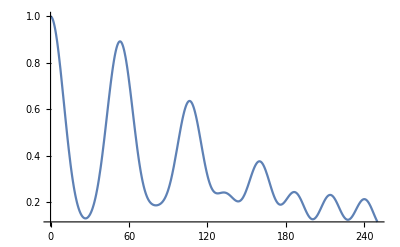

```mathematica
Plot[{P01}//.subNum,{t,0,250}]
```

```mathematica
R=Eigenvectors[δ*({{-1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})+gf*({{0, √n0, √n0, 0}, {√n0, 0, 0, √(n0-1)}, {√n0, 0, 0, √(n0-1)}, {0, √(n0-1), √(n0-1), 0}})//.subNum]//Transpose

En=Eigenvalues[δ*({{-1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})+gf*({{0, √n0, √n0, 0}, {√n0, 0, 0, √(n0-1)}, {√n0, 0, 0, √(n0-1)}, {0, √(n0-1), √(n0-1), 0}})//.subNum]
```

(0.801825 | -0.219504 | -0.555783 | 0.
-0.401969 | -0.400827 | -0.421614 | 0.707107
-0.401969 | -0.400827 | -0.421614 | -0.707107
0.184168 | -0.794036 | 0.5793 | 0.)

{-0.0239152,0.0226322,0.00128303,0.}

```mathematica
CoefNum=c[2,2,R,ρ0]
ΩNum=W[En]
```

(0.0261079 | 0.0259597 | 0.0287221 | 0.0807896
0.0259597 | 0.0258123 | 0.0285591 | 0.080331
0.0287221 | 0.0285591 | 0.0315981 | 0.0888793
0.0807896 | 0.080331 | 0.0888793 | 0.25)

(0. | -0.0465475 | -0.0251983 | -0.0239152
0.0465475 | 0. | 0.0213492 | 0.0226322
0.0251983 | -0.0213492 | 0. | 0.00128303
0.0239152 | -0.0226322 | -0.00128303 | 0.)

0.177759 cos(0.00806149 t)+0.0571181 cos(0.134141 t)+0.160662 cos(0.142202 t)+0.161579 cos(0.150264 t)+0.0574442 cos(0.158325 t)+0.0519193 cos(0.292466 t)+0.333518

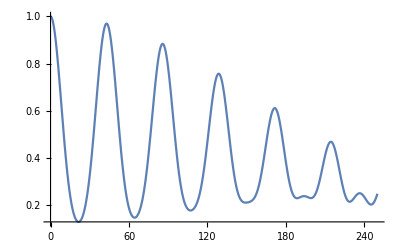

```mathematica
P01Num=Sum[CoefNum[[j,k]]*Cos[2π*ΩNum[[j,k]]*t],{j,4},{k,4}]
Plot[P01Num,{t,0,250}]
```